# Mass of an Isothermal (pressure bounded) Atmosphere

```mathematica
Quit
```

## Basic mass integral

In units of the bondi radius the density (relative to 1 for background density) is

```mathematica
ρ = Exp[1/r -1/nB]
```

assuming the backround density is reachs at r = nB.  The mass integral has the basic scaling:

```mathematica
4π Integrate[Exp[1/r] r^2,r]
```

2/3 π (ⅇ^(1/r) r (1+r+2 r^2)-ExpIntegralEi[1/r])

For an atmosphere that extends from an inner radius rcb < 1 to nB (both in Bondi radii) the mass integral is below.  The prefactor e^(-1/nB) has been pulled out

```mathematica
Miso = 4π Exp[-1/nB] Assuming [0< rcb < nB,Integrate[Exp[1/r] r^2,{r, rcb, nB}]]
```

2/3 ⅇ^(-1/nB) π (ⅇ^(1/nB) nB (1+nB+2 nB^2)-ⅇ^(1/rcb) rcb (1+rcb+2 rcb^2)-ExpIntegralEi[1/nB]+ExpIntegralEi[1/rcb])

```mathematica
miso[rcb_, nB_] := (2 π)/6 ⅇ^(-1/nB) (ⅇ^(1/nB) nB (1+nB+2 nB^2)-ⅇ^(1/rcb) rcb (1+rcb+2 rcb^2)-ExpIntegralEi[1/nB]+ExpIntegralEi[1/rcb])
```

compare to the integral to the analytic rcb << 1 scaling miso ~ 4 π rhocb rcb^4,

```mathematica
(*using ρcb = Exp[1/rcb-1/nB];*)
It[rcb_, nB_] := miso[rcb, nB]/(4 π Exp[1/rcb-1/nB] rcb^4)
```

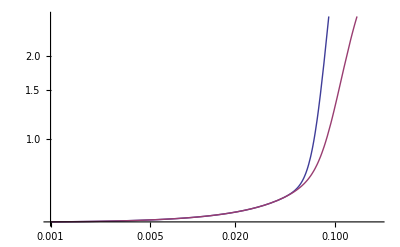

```mathematica
LogLogPlot[{It[rcb,3], It[rcb,1]},{rcb,.001,.2}]
```

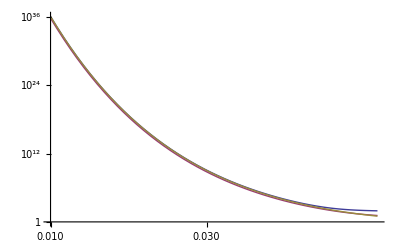

```mathematica
LogLogPlot[{miso[rcb,3], miso[rcb,1], 4π Exp[1/rcb - 1] rcb^4},{rcb,.01,.1}]
```

## Divergence

The following shows that the mass exterior to Bondi radius diverges for a large external radius, even when the background density is subtracted off (the -1 after the exponential

```mathematica
Iout = Assuming[nB > 1,Integrate[3(Exp[1/r - 1/nB]-1)r^2,{r, 1, nB}]]
```

1/2 (2+nB+nB^2+ⅇ^(-1/nB) (-4 ⅇ+ExpIntegralEi[1]-ExpIntegralEi[1/nB]))

```mathematica
Limit[Iout/nB^2, nB -> ∞]
```

1/2

## More scalings

older efforts that did the same thing

```mathematica
Assuming[1> θc > 0,Integrate[Exp[1/x] x^2,{x,θc,1}]]
```

1/6 (4 ⅇ-ⅇ^(1/θc) θc (1+θc+2 θc^2)-ExpIntegralEi[1]+ExpIntegralEi[1/θc])

```mathematica
Assuming[1> θc > 0,Series[%2,{θc,0,4}]]
```

1/6 (4 ⅇ-ExpIntegralEi[1]+ⅇ^(1/θc) (-θc-θc^2-2 θc^3+O[θc]^5)+ⅇ^(1/θc) (θc+θc^2+2 θc^3+6 θc^4+O[θc]^5))

```mathematica
N[1/6 (4 ⅇ-ExpIntegralEi[1]+ⅈ π Floor[-Arg[θc]/(2 π)]-ⅈ π Floor[Arg[θc]/(2 π)]+ⅈ π Floor[(π+Arg[θc])/(2 π)]) /. θc-> .001]
```

1.49633

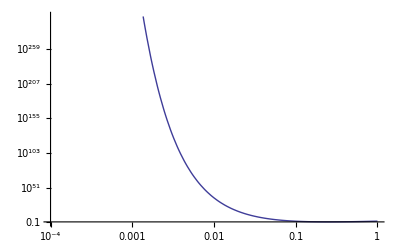

```mathematica
LogLogPlot[θc^4 Exp[1/θc],{θc,.0001,1}]
```